```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Folgendes Integral soll minimiert bzw. maximiert (Vorzeichen des Integrandens wird invertiert) werden:

ℐ=∫_t_1^t_2 F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→min , bzw.  ℐ=∫_t_1^t_2 -F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→max

In dem Funktionenvektor 𝓏_1 sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) vorkommen.
In dem Funktionenvektor 𝓏_2 hingegen sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) nicht vorkommen. 𝓏_2 ist in der Regel ausschließlich im 3. Fall vorhanden!

2. Fall: Ein weiteres Integral soll einen festen Wert τ annehmen:

τ=∫_t_1^t_2 G(t,𝓏_1, (𝓏̇)_1)ⅆt

Für das resultierende Differentialgleichungssystem gilt:

H(t,𝓏_1, (𝓏̇)_1,λ)=F(t,𝓏_1, (𝓏̇)_1)+λ G(t,𝓏_1, (𝓏̇)_1)
0=∇_𝓏_1 H(t,𝓏_1, (𝓏̇)_1,λ)-ⅆ/ⅆt∇_((𝓏̇)_1) H(t,𝓏_1, (𝓏̇)_1,λ)

## Eingabe (F, 𝓏_1, 𝓏_2, 𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃, G)

```mathematica
ClearAll["Global`*"]
F[x_]=y[x];
𝓏1[x_]={y[x]};
𝓏2[x_]={};
𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃={y[0]==0,y[X]==0};
G[x_]=√(1+D[y[x],x]^2);
```

## Programm (automatisch)

```mathematica
(*Programm*)
<<VariationalMethods`
H[x_]=F[x]+λAllgemein G[x];
𝓏[x_]=Join[𝓏1[x],𝓏2[x]];
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽=Table[
FullSimplify[VariationalD[H[x],𝓏[x],x]][[i]]==0,
{i,Length[𝓏[x]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽//TableForm]]
```

1-(λAllgemein y''[x])/((1+y'[x]^2)^(3/2))==0

## Programm (manuell)

```mathematica
(*Programm*)
H[x_]=F[x]+λAllgemein G[x];
𝓏[x_]=Join[𝓏1[x],𝓏2[x]];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ=Table[
FullSimplify[(Grad[H[x],𝓏[x]]-D[Grad[H[x],D[𝓏[x],x]],x])][[i]]==0,
{i,Length[𝓏[x]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm]]
```

1-(λAllgemein y''[x])/((1+y'[x]^2)^(3/2))==0

0=1-(λAllgemein y''[x])/((1+y'[x]^2)^(3/2))
0=(1+y'[x]^2)^(3/2)-λAllgemein y''[x]

```mathematica
(*Programm*)
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ={(1+y'[x]^2)^(3/2)-λAllgemein y''[x]==0};

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm]]
```

(1+y'[x]^2)^(3/2)-λAllgemein y''[x]==0

## Programm (Differentialgleichung)

```mathematica
(*Programm*)
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x_]=Flatten[FullSimplify[N[DSolve[Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ,𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],𝓏[x],x]]]][[All,2]];

(*Ausgabe*)
Print[StringForm["𝓎_allgemein(x) = ``",
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x]//MatrixForm]]
```

𝓎_allgemein(x) = ((0.-0.5 ⅈ) (√(X^2-4. λAllgemein^2)-1. √(4. x^2-4. x X+X^2-4. λAllgemein^2))
(0.+0.5 ⅈ) (√(X^2-4. λAllgemein^2)-1. √(4. x^2-4. x X+X^2-4. λAllgemein^2)))

y_allgemein(x)=±0.5 ⅈ (√(X^2-4 λAllgemein^2)-√(4 x^2-4x X+X^2-4 λAllgemein^2))

```mathematica
Print[Factor[4 x^2-4x X+X^2]]
```

(2 x-X)^2

y_allgemein(x)=±0.5 ⅈ (√(X^2-4 λAllgemein^2)-√((2 x-X)^2-4 λAllgemein^2))
y_allgemein(x)=±0.5 √-1 (√(X^2-4 λAllgemein^2)-√((2 x-X)^2-4 λAllgemein^2))
y_allgemein(x)=±0.5 (√(-1(X^2-4 λAllgemein^2))-√(-1((2 x-X)^2-4 λAllgemein^2)))
y_allgemein(x)=±0.5 (√(4 λAllgemein^2-X^2)-√(4 λAllgemein^2-(2 x-X)^2))

```mathematica
(*Programm*)
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x_]={.5(√(4 λAllgemein^2-X^2)-√(4 λAllgemein^2-(2 x-X)^2)),-.5(√(4 λAllgemein^2-X^2)-√(4 λAllgemein^2-(2 x-X)^2))};

(*Ausgabe*)
Print[StringForm["𝓎_allgemein(x) = ``",
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x]//MatrixForm]]
```

𝓎_allgemein(x) = (0.5 (-√(-(2 x-X)^2+4 λAllgemein^2)+√(-X^2+4 λAllgemein^2))
-0.5 (-√(-(2 x-X)^2+4 λAllgemein^2)+√(-X^2+4 λAllgemein^2)))

## Programm (λ)

X beträgt 1. Für y_allgemein(x) gilt dann (das ± entfällt bei der Quadrierung in G(x)):

```mathematica
(*Programm*)
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x_]={.5(√(4 λAllgemein^2-1)-√(4 λAllgemein^2-(2 x-1)^2)),-.5(√(4 λAllgemein^2-1)-√(4 λAllgemein^2-(2 x-1)^2))};

(*Ausgabe*)
Print[StringForm["𝓎_allgemein(x) = ``",
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x]//MatrixForm]]
```

𝓎_allgemein(x) = (0.5 (√(-1+4 λAllgemein^2)-√(-(-1+2 x)^2+4 λAllgemein^2))
-0.5 (√(-1+4 λAllgemein^2)-√(-(-1+2 x)^2+4 λAllgemein^2)))

```mathematica
Print[FullSimplify[D[±.5(√(4 λAllgemein^2-1)-√(4 λAllgemein^2-(2 x-1)^2)),x]^2]]
```

-(4 (1-2 x)^2 (±0.5)^2)/((1-2 x)^2-4 λAllgemein^2)

y_allgemein(x)=(-(1-2 x)^2)/((1-2 x)^2-4 λAllgemein^2)

𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽 entspricht den Integrationsgrenzen bzw. den Nebenbedingungen:

```mathematica
G=√(1-(1-2 x)^2/((1-2 x)^2-4 λAllgemein^2));
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,1};
```

```mathematica
$Assumptions=λAllgemein∈Reals;
Print[Integrate[G,{x,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]}]]
```

ConditionalExpression[2 Abs[λAllgemein] ArcTan[1/(√(-1+4 λAllgemein^2))], 4 λAllgemein^2>1]

Solve[…] funktioniert nicht, daher wird Newton’sches Verfahren (FindRoot[…])  verwendet:

τ=1.2=2 Abs[λAllgemein] ArcTan[1/(√(-1+4 λAllgemein^2))]
0=Abs[λAllgemein] ArcTan[1/(√(-1+4 λAllgemein^2))]-0.6

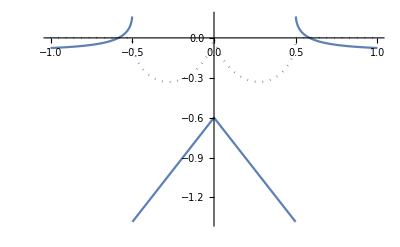

```mathematica
Print[ReImPlot[Abs[λAllgemein] ArcTan[1/(√(-1+4 λAllgemein^2))]-0.6,{λAllgemein,-1,1},PlotRange->All]]
```

Nur die positive Lösung für λ relevant, da λ in der Differentialgleichung quadriert wird:

```mathematica
λ=λAllgemein/.FindRoot[Abs[λAllgemein] ArcTan[1/(√(-1+4 λAllgemein^2))]-0.6,{λAllgemein,.6}]
```

0.584375

```mathematica
(*Programm*)
𝓎[x_]=FullSimplify[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x]/.λAllgemein->λ];

(*Ausgabe*)
Print[StringForm["λ = ``\n𝓎(x) = ``",
λ,
𝓎[x]//MatrixForm]]
```

λ = 0.584375
𝓎(x) = (0.30248-0.5 √(0.365976-4 (-1+x) x)
-0.30248+0.5 √(0.365976-4 (-1+x) x))

## Plot

𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽 entspricht den Integrationsgrenzen bzw. den Nebenbedingungen:

```mathematica
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,1};
```

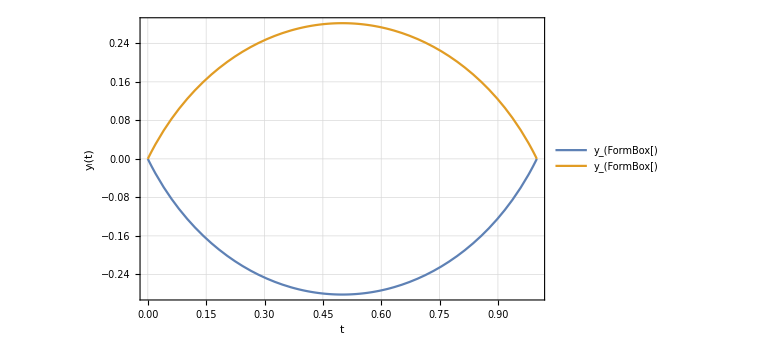

```mathematica
(*Ausgabe*)
plot=Plot[Evaluate[𝓎[t]],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
ImageSize->Large];
Print[Show[plot]]
```